```mathematica
Practical 2
Aim:Secant Method and Regula Falsi Method
```

```mathematica
1. SECANT METHOD
```

```mathematica
Example 1 
Use secant method to determine the roots of the equation  f(x)=1.15-1.04*x+Log[x], taking initial approximation as x=1,x1=2
```

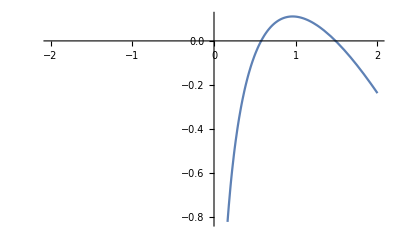

```mathematica
secant[f_,ao_,bo_,n_]:=Module[{},p0=N[ao];p1=N[bo];
If[f[p0]*f[p1]>0,Print["Secant method cannot applied"];
Return[]];
i=1;
While[i≤n,p2=N[p1-((p1-p0)*f[p1]/(f[p1]-f[p0]))];
Print[i,"  ",p0,"  ",p1];
i++;
p0=p1;
p1=p2];
Print["Roots=",p2]]
f[x_]:=1.15-1.04*x+Log[x];
Plot[f[x],{x,-2,2}]
```

```mathematica
secant[f,1,2,5]
```

1  1.  2.

2  2.  1.31714

3  1.31714  1.44703

4  1.44703  1.49325

5  1.49325  1.48762

Roots=1.48776

```mathematica
Example 2
Use secant method to determine the roots of the equation  f(x)= -2*x^2+x+3, taking initial approximation as x=0,x1=-2
```

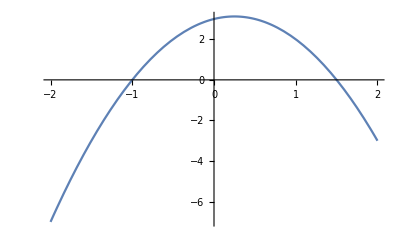

```mathematica
f[x_]:=-2*x^2+x+3;
Plot[f[x],{x,-2,2}]
```

```mathematica
secant[f,-0,2,5]
```

1  0.  2.

2  2.  1.

3  1.  1.4

4  1.4  1.52632

5  1.52632  1.49892

Roots=1.49999

```mathematica
Example 3
Use secant method to determine the roots of the equation f(x)= E^x-3*x, taking initial approximation as x=0,x1=1
```

3 Example

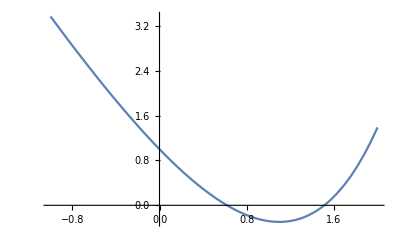

```mathematica
h[x_]:=E^x-3*x;
Plot[h[x],{x,-1,2}]
```

```mathematica
secant[h,0,1,5]
```

1  0.  1.

2  1.  0.780203

3  0.780203  0.496679

4  0.496679  0.635952

5  0.635952  0.62056

Roots=0.61904

```mathematica
2. REGULA FALSI METHOD
```

```mathematica
Example 1 
Use  Regula Falsi  method to determine the roots of the equation  f(x)=x ^ 3+ 3 * x - 3, taking initial approximation as x=1,x1=2
```

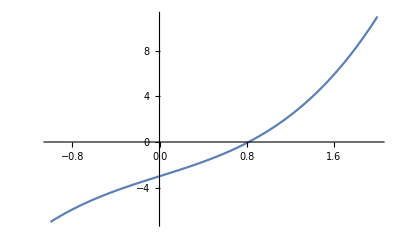

```mathematica
RegulaFalsi [f_,ao_, bo_, n_] := Module[{}, x = N[ao];
y = N[bo];
u = (x * f[y] - y * f[x]) / (f[y] - f[x]);
k = N[n];
While[k < 1, If[Sign[f[y]] == Sign[f[u]], u = y, x = u];
u = (x* f[y] - y * f[x]) / (f[y] - f[x]);
k = k + 1];
Print["u =", NumberForm [u, 16]];
Print["f[u] =" NumberForm [f[u], 16]];]
 f[x_] := x ^ 3+ 3 * x - 3;
Plot[f[x], {x, - 1, 2}]
```

```mathematica
RegulaFalsi[f,1,2,5]
```

u =0.9

f[u] = 0.4290000000000003

```mathematica
Example 2
Use  Regula Falsi  method to determine the roots of the equation f(x)=  Sin[x]-x^2*E^x, taking initial approximation as x=0,x1=2
```

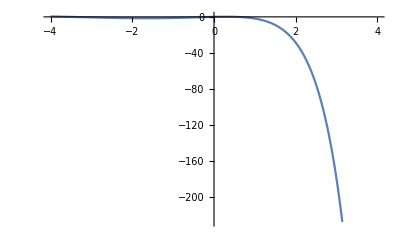

```mathematica
f[x_]:=Sin[x]-x^2*E^x;
Plot[f[x],{x,-4,4}]
```

```mathematica
RegulaFalsi[f,0,2,5]
```

u =0.

f[u] = 0.

```mathematica
Example 3
Use  Regula Falsi  method to determine the roots of the equation  f(x)=x^3-5*x^2+2*x+1 , taking initial approximation as x=0,x1=3
```

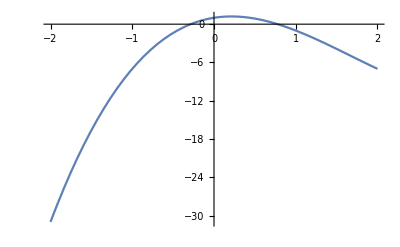

```mathematica
f[x_]:=x^3-5*x^2+2*x+1;
Plot[f[x],{x,-2,2}]
```

```mathematica
RegulaFalsi[f,0,3,4]
```

u =0.25

f[u] = 1.203125